# GWMMatch - 02 : Power Spectral Densities

GWMMatch currently has over 20 built-in detector noise curves spanning ground-based interferometers (initial LIGO/Virgo through next-generation CE and ET) and the space-based LISA mission.

### 0. Preamble

#### Load Package

```mathematica
<<GWMMatch`
```

#### Grid parameters shared by all plots

```mathematica
deltaF=0.5;   (*Hz bin spacing*)
fLow=1.0;   (*Hz—low enough to cover LISA and ET*)
nFreq=8193;  (*covers up to 4096 Hz at 0.5 Hz spacing*)

freqs=Table[(k-1)*deltaF,{k,1,nFreq}];
```

### 1. All available models

```mathematica
allModels=ListDetectorPSDs[];
Print["Available PSD models (",Length[allModels],"):"];
Print[Column[allModels]];
```

Available PSD models (19):

aLIGOZeroDetHighPower
aLIGOZeroDetLowPower
aLIGONSNSOpt
aLIGOBHBH20Deg
aLIGOHighFrequency
AdvVirgo
KAGRA
Virgo
iLIGOSRD
EinsteinTelescopeP1600143
CosmicExplorerP1600143
CosmicExplorerPessimisticP1600143
CosmicExplorerWidebandP1600143
aLIGOZeroDetHighPowerGWINC
LISA
LISAConfusion05yr
LISAConfusion1yr
LISAConfusion2yr
LISAConfusion4yr

### 2. aLIGO: analytical vs tabulated comparison

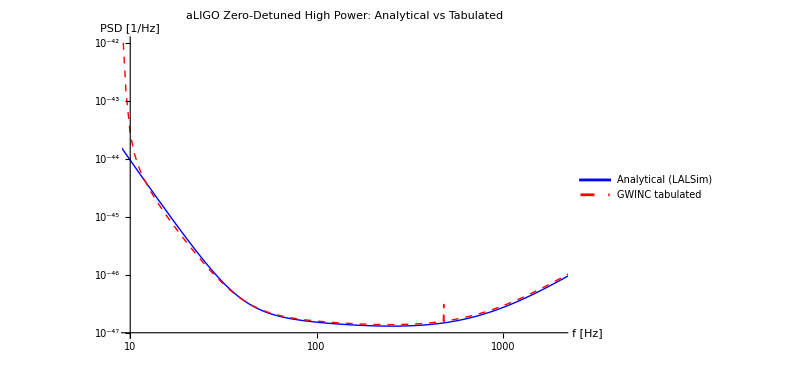

```mathematica
psdAnalytical=DetectorPSD["aLIGOZeroDetHighPower",nFreq,deltaF,fLow];
psdGWINC=DetectorPSD["aLIGOZeroDetHighPowerGWINC",nFreq,deltaF,fLow];

plotALIGO=ListLogLogPlot[{Transpose[{freqs,psdAnalytical}],Transpose[{freqs,psdGWINC}]},Joined-> True,PlotStyle->{{Blue,Thick},{Red,Dashed,Thick}},PlotLegends->Placed[LineLegend[{"Analytical (LALSim)","GWINC tabulated"},LegendMarkerSize->30],{0.7,0.25}],PlotLabel->"aLIGO Zero-Detuned High Power: Analytical vs Tabulated",AxesLabel->{"f [Hz]","PSD [1/Hz]"},PlotRange->{{10,2000},{1*^-42,1*^-47}},GridLines->Automatic,GridLinesStyle->LightGray,ImageSize->600]
```

### 3. Next-generation ground-based: ET and CE variants

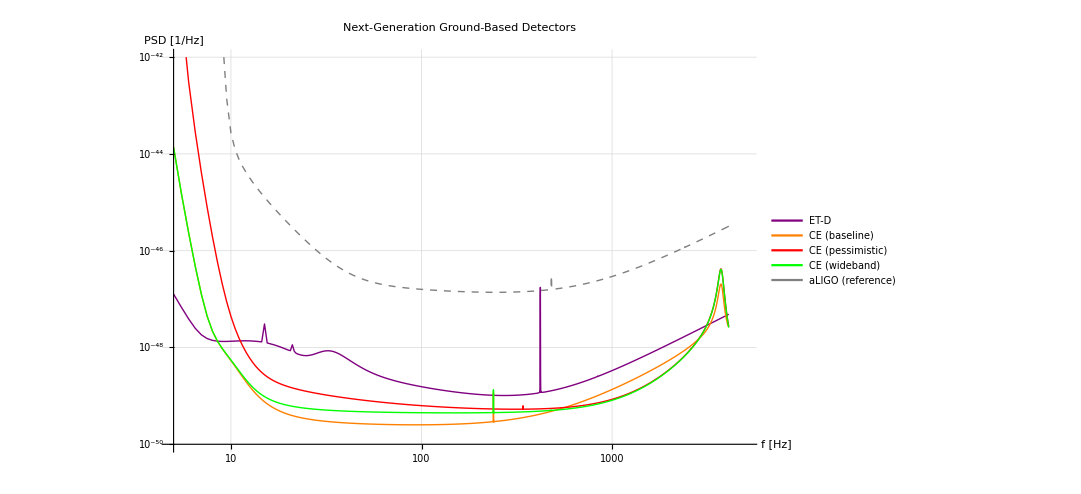

```mathematica
ngModels={"EinsteinTelescopeP1600143","CosmicExplorerP1600143","CosmicExplorerPessimisticP1600143","CosmicExplorerWidebandP1600143"};
ngLabels={"ET-D","CE (baseline)","CE (pessimistic)","CE (wideband)"};
ngColors={Purple,Orange,Red,Green};

plotNG=Show[Table[With[{psd=DetectorPSD[ngModels[[i]],nFreq,deltaF,fLow],col=ngColors[[i]]},
ListLogLogPlot[Transpose[{freqs,psd}],Joined->True,PlotStyle->{col,Thick},PlotLegends->None,PlotRange->{{5,5000},{1*^-42,1*^-50}}]],{i,Length[ngModels]}],(*Overlay the aLIGO tabulated curve for reference*)
ListLogLogPlot[Transpose[{freqs,psdGWINC}],Joined->True,PlotStyle->{Gray,Dashed,Thick},PlotRange->{{5,5000},{1*^-42,1*^-50}},PlotLegends->Placed[LineLegend[Append[ngColors,Gray],Append[ngLabels,"aLIGO (reference)"],LegendMarkerSize->30],{Center, Top}]],PlotLabel->"Next-Generation Ground-Based Detectors",AxesLabel->{"f [Hz]","PSD [1/Hz]"},GridLines->Automatic,GridLinesStyle->LightGray,ImageSize->800]
```

### 4. LISA: effect of galactic confusion noise

-- LISA: galactic confusion noise --

General::munfl: Exp[-708.546] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-709.848] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-709.504] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

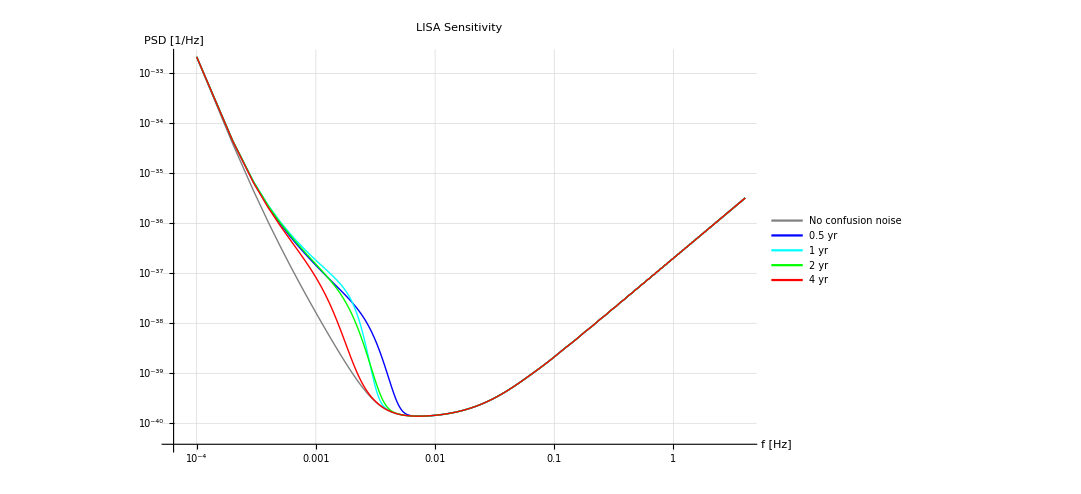

```mathematica
Print["-- LISA: galactic confusion noise --"];

lisaDeltaF=1.0*^-4;  (*0.1 mHz spacing for LISA band*)
lisaNFreq=40001;    (*up to 4 Hz*)
lisaFLow=1.0*^-4;

lisaFreqs=Table[(k-1)*lisaDeltaF,{k,1,lisaNFreq}];

lisaModels={"LISA","LISAConfusion05yr","LISAConfusion1yr","LISAConfusion2yr","LISAConfusion4yr"};
lisaLabels={"No confusion noise","0.5 yr","1 yr","2 yr","4 yr"};
lisaColors={Gray,Blue,Cyan,Green,Red};

plotLISA=Legended[Show[Table[With[{psd=DetectorPSD[lisaModels[[i]],lisaNFreq,lisaDeltaF,lisaFLow],col=lisaColors[[i]]},
ListLogLogPlot[Transpose[{lisaFreqs,psd}],Joined->True,PlotStyle->{col,Thick},PlotLegends->None(*,PlotRange->{{5,5000},{1*^-42,1*^-50}}*)]],{i,Length[lisaModels]}],PlotLabel->"LISA Sensitivity",AxesLabel->{"f [Hz]","PSD [1/Hz]"},GridLines->Automatic,GridLinesStyle->LightGray,ImageSize->800],Placed[LineLegend[lisaColors,lisaLabels,LegendMarkerSize->30],{Center, Top}]]
```